```mathematica
SetDirectory[NotebookDirectory[]];
DSolve[{y'[x]==-2x y[x] ,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(-x^2)}}

```mathematica
{{y[x]->ⅇ^(-x^2)}}
```

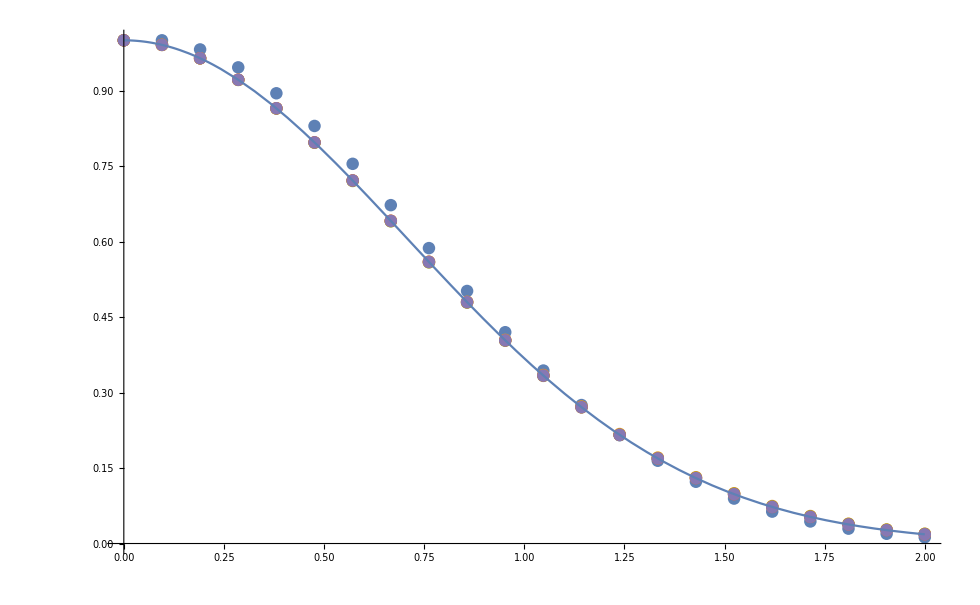

```mathematica
Euler=Import["euler.txt","Table"];
Huen=Import["huen.txt","Table"];
MidPoint=Import["midpoint.txt","Table"];
RK4=Import["rk4.txt","Table"];
PredCor=Import["predcor.txt","Table"];
anal=Plot[Exp[-x^2],{x,0,2}];

plots = ListPlot[{Euler,Huen,MidPoint,RK4,PredCor}];
Show[plots,anal]
```

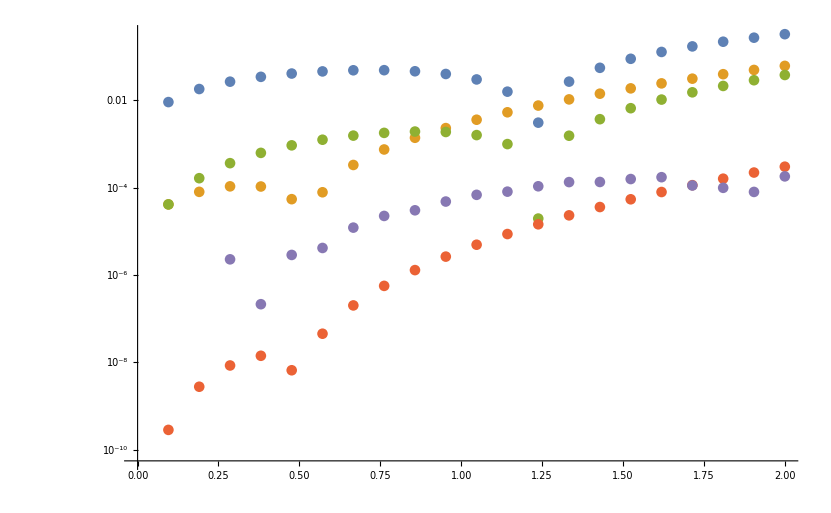

```mathematica
EulerEr=Import["eulererror.txt","Table"];
HuenEr=Import["huenerror.txt","Table"];
MidPointEr=Import["midpointerror.txt","Table"];
RK4Er=Import["rk4error.txt","Table"];
PredCorEr=Import["predcorerror.txt","Table"];
ListLogPlot[{EulerEr,HuenEr,MidPointEr,RK4Er,PredCorEr}]
```

```mathematica
ListPlot[Import["sol1ty.txt","Table"]]
ListPlot[Import["sol1vy.txt"],"Table"]
```

Import::nffil: File sol1ty.txt not found during Import.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed]

Import::nffil: File sol1vy.txt not found during Import.

ListPlot::nonopt: Options expected (instead of Table) beyond position 1 in ListPlot[$Failed,Table]. An option must be a rule or a list of rules.

ListPlot[$Failed,Table]